lpw

```mathematica
(* Mathematica notebook for spectra. Following [Esarey]'s paper in sections A. and B.
  date : 04/03/2019
  author: Óscar L. Amaro
*)
```

A. Linear polarization p. 3007

```mathematica
(*Parameters*)
γ0=5; (*p. 48*)
a0=0.5;
N0=7;

β0=√(1-1/γ0^2); (*normalizations*)
c=1;
ω0=1;
k0=ω0/c;

h0=γ0(1+β0); (* p.3006 (8c)*)

k=ω/c;(*p.3007 (26)*) 
L0=(2 π)/ω0*β0; (*much larger than 1/k0???*)
η0=L0/2;

r1=a0 / (h0 k0); (*p. 3006 (16a)*)
z1=-a0^2 / (8 h0^2 k0);
β1=(1-1/M0)/2;
M0=h0^2/(1+a0^2/2);
```

```mathematica
(*Functions p. 3008*)
kbar=Function[{θ,n,k},k(1-β1(1+Cos[θ]))-n k0];(*(30a)*)

(*alpha*)
αz=Function[{θ,ϕ,n},(n a0^2 (1+Cos[θ]))/(8 h0^2 (1-β1(1+Cos[θ])))];(*(38a)*)
αx=Function[{θ,ϕ,n},(n a0 Sin[θ]Cos[ϕ])/(h0(1-β1(1+Cos[θ])))];(*(38b)*)
(*C*)
sumlim=10; (*parameter that controls the sum*)
Cx=Function[{θ,ϕ,n},
k0 r1 Sum[(-1)^m BesselJ[m,αz[θ,ϕ,n]] (BesselJ[n-2 m-1,αx[θ,ϕ,n]]+BesselJ[n-2 m +1,αx[θ,ϕ,n]]),
{m,-sumlim,sumlim}]];(*(37a)*)
Cz=Function[{θ,ϕ,n},
2 Sum[(-1)^m  BesselJ[m,αz[θ,ϕ,n]] (β1*BesselJ[n-2 m,αx[θ,ϕ,n]]+k0 z1 (
BesselJ[n-2 m -2,αx[θ,ϕ,n]]+BesselJ[n-2 m +2,αx[θ,ϕ,n]] ) ),
{m,-sumlim,sumlim}]] ;(*(37b)*)

(*main*)
dIdωdΩ=Function[{ω,θ,ϕ},
k^2/(4 π^2) Sum[ (Sin[kbar[θ,n,k] η0 ]/(kbar[θ,n,k] η0))^2((Cx[θ,ϕ,n]^2) (1-Sin[θ]^2 Cos[ϕ]^2)+Cz[θ,ϕ,n]^2 Sin[θ]^2 - Cx[θ,ϕ,n] Cz[θ,ϕ,n] Sin[2 θ] Cos[ϕ])
,{n,1,10}]]; (*(36*)
```

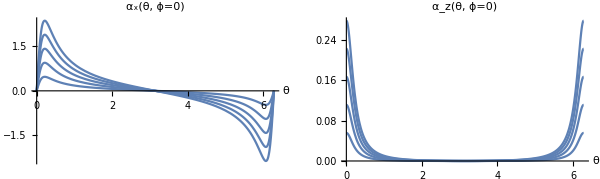

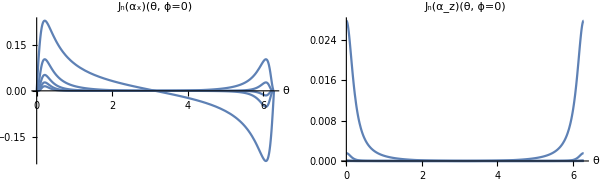

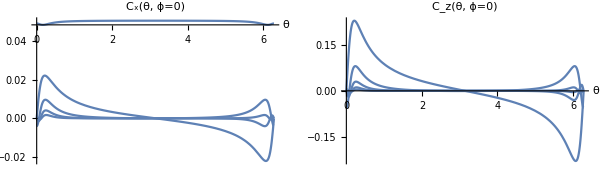

```mathematica
(*Auxiliary functions*)
fig1=Show[Table[Plot[αx[θ,0,n],{θ,0,2 π},PlotLabel->"α_x(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
fig2=Show[Table[Plot[αz[θ,0,n],{θ,0,2 π},PlotLabel->"α_z(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
GraphicsRow[{fig1,fig2},ImageSize->600]

fig1=Show[Table[Plot[BesselJ[n,αx[θ,0,n]],{θ,0,2 π},PlotLabel->"J_n(α_x)(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
fig2=Show[Table[Plot[BesselJ[n,αz[θ,0,n]],{θ,0,2 π},PlotLabel->"J_n(α_z)(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
GraphicsRow[{fig1,fig2},ImageSize->600]

fig1=Show[Table[Plot[Cx[θ,0,n],{θ,0,2 π},PlotLabel->"C_x(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
fig2=Show[Table[Plot[Cz[θ,0,n],{θ,0,2 π},PlotLabel->"C_z(θ, ϕ=0)",PlotRange->All,AxesLabel->{"θ",""}],{n,1,5}]];
GraphicsRow[{fig1,fig2},ImageSize->600]
```

```mathematica
(*1d*)
lst=Table[{y,dIdωdΩ[4 γ0^2 ω0 y,0,0]/.ω->( 4 γ0^2 ω0 y)},{y,0.01,2.5,0.01}];
```

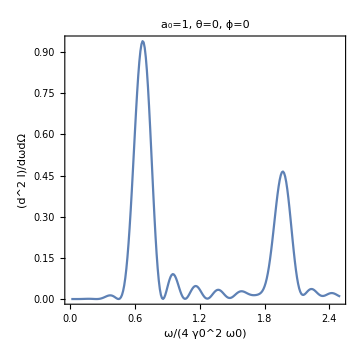

```mathematica
ListPlot[lst,ImageSize->Medium,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"ω/(4 γ0^2 ω0)","(d^2  I)/dωdΩ"},PlotLabel->"a_0="<>ToString[a0] <>", θ=0, ϕ=0",PlotRange->All]
```

```mathematica
(*2d*)
tab=Table[{y,gθ,dIdωdΩ[4 γ0^2 ω0 y,gθ/γ0,0]/.ω-> (4 γ0^2 ω0  y)},{y,0.01,3,0.05},{gθ,0,1,0.05}];
Dimensions[tab]
```

{60,21,3}

```mathematica
ListPlot3D[Flatten[tab,1],PlotLabel->"a_0="<>ToString[a0] ,AxesLabel->{"ω/(4 γ0^2 ω0)","γ_0 θ","(d^2  I)/dωdΩ"},PlotRange->All]
```

-Graphics3D-

Fig 2:  Normalized intensity (a_0=5, N_0=7, ϕ = 0)

```mathematica
(*Solve for variable in horizontal axis. Keep the largest root.*)
Clear[y]
Solve[y==(a0^2/4)(1+a0^2/2),a0][[4,1,2]] (*the article is somewhat ambiguous*)
```

√(-1+√(1+8 y))

```mathematica
(*Define functions*)
Clear[n]
αn = Function[{n,a0},(n a0^2/4)(1+a0^2/2)];
Fn=Function[{n,a0},n αn[n,a0] (BesselJ[(n-1)/2,αn[n,a0]]-BesselJ[(n+1)/2,αn[n,a0]])^2];
```

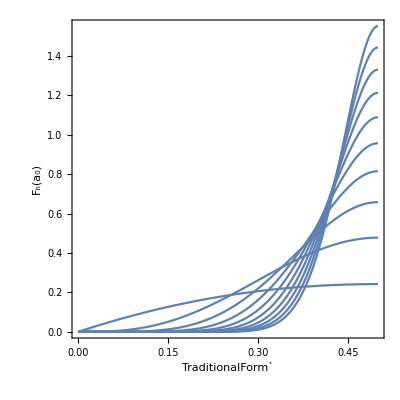

```mathematica
(*Plot*)
Show[Table[Plot[Fn[n,√(-1+√(1+8 y))],{y,0,0.5},AspectRatio->1,Frame->True,PlotRange->All,
FrameLabel->{"TraditionalForm`","F_n(a_0)"}],{n,1,19,2}]]
```

Fig 4: F_n(a_0) as a function of a_0^2/4 (1+a_0^2/2)

B. Circular polarization p. 3010

```mathematica
Y=Function[ ξ,ξ^2 BesselK[2/3,ξ]^2];
```

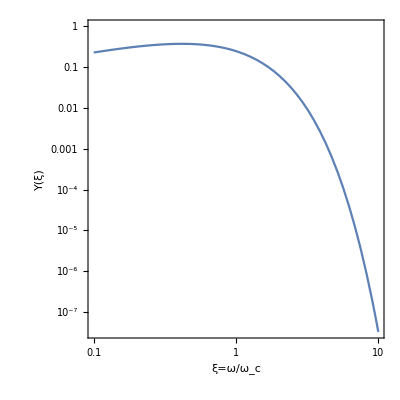

```mathematica
LogLogPlot[Y[ξ],{ξ,10^-1,10^1},AspectRatio->1,Frame->True,FrameLabel->{"ξ=ω/ω_c","Y(ξ)"}]
```

Fig 7: Y= ξ^2 K_(2/3)((ξ))^2

2. Linear polarization p. 3014

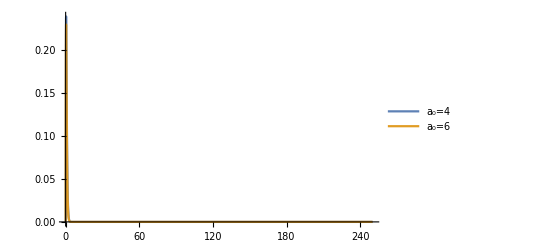

```mathematica
(*FIG 8*)
Clear[a0]

h0=1;(*arbitrário?*)
ω0=1;
γ0=5;
M0=1;(*arbitrário?*)
nc=3 a0^3 /(2√2); (*approx*)
γ=(a0 (M0+1))/(2 (2 M0)^0.5);
ωc=nc (M0+1) ω0/2;
ξ=ω/ωc(1+γ^2θ^2)^1.5;
ωNOR=ω/ω0;
d2IdodO=Function[{ωNOR,a1},(γ^2 ξ^2)/(1+γ^2 θ^2)((γ^2 θ^2)/(1+γ^2 θ^2) BesselK[1/3,ξ]^2+BesselK[2/3,ξ]^2)/.a0->a1];
θ=Pi/2;
Plot[{d2IdodO[ωNOR,6],d2IdodO[ωNOR,4]},{ω,0,250},PlotRange->All,PlotLegends->Placed[{"a_0=4","a_0=6"},Above]]
```

Fig 8:

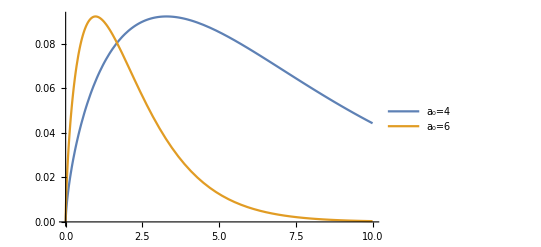

```mathematica
Clear[a0]

h0=1;(*arbitrário?*)
ω0=1;
γ0=5;
M0=0.1; (*arbitrário?*)
nc=3 a0^3 /4; (*approx*)
γh=h0/2;
ωc=nc M0 ω0;
ζ=ω/ωc(1+γh^2θ^2)^1.5;
ωNOR=ω/(4γ0^2ω0^2);
d2IdodO=Function[{ωNOR,a1},(γh^2 ζ^2)/(1+γh^2 θ^2)((γh^2 θ^2)/(1+γh^2 θ^2) BesselK[1/3,ζ]^2+BesselK[2/3,ζ]^2)/.a0->a1];
θ=0;
Plot[{d2IdodO[ωNOR,6],d2IdodO[ωNOR,4]},{ω,0,10},PlotRange->All,PlotLegends->Placed[{"a_0=4","a_0=6"},Above]]
```

```mathematica
(*where to look for harmonics*)
```

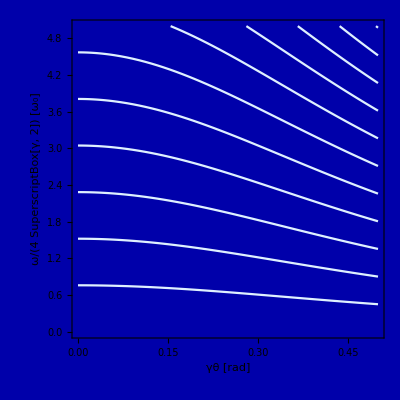

```mathematica
γ0=2;
a0=0.1;

ω0=1;
β0=√(1-1/γ0^2);M0=γ0^2 (1+β0^2)^2 / (1+a0^2/2);β1=(1-1/M0)/2;
ωn[θ_,n_]:=(n ω0)/(1-β1 (1+Cos[θ]))

Show[  Table[Plot[ωn[θ,n]/(4 γ0^2),{θ,0,1/γ0},PlotRange->{0,5},PlotStyle->LightBlue,AspectRatio->1,Axes->False,Frame->True,FrameLabel->{Text[Style["γθ [rad]",White,25]],Text[Style["ω/(4 SuperscriptBox[γ, 2]) [ω_0]",White,25]]},Background->Darker[Blue]],{n,1,30,1}]  ]
```

lpw

```mathematica
(* Mathematica notebook for trajetory in linear polarized plane wave. Following [Esarey]'s paper in section II. Electron Motion in Intense Laser Fields (p. 3005) 1) Linear Polarization
  date : 17/01/2019
  author: Óscar L. Amaro
*)
```

```mathematica
(*Parameters*)
N0=7;
dt=0.1/8;
tmax=Round[N0* 2π/dt]; (* normalized time*)
η=Table[t*dt,{t,1,tmax,1}]; (*eta*)

a0=1; (*normalized amplitude*)
δp=0; (*1-linear, 0-circular*)
γ0=5; (*initial gamma *)
γ0L=γ0/(1+a0^2/2); (*average gamma *)
β0=Sqrt[1-1/(γ0*γ0)]; (*initial β *)
h0=γ0 (1+β0);
k0=1;
M0=h0^2/(1+a0^2/2);

(*p.3006*)
r1=a0/(h0 k0);
z1 = -a0^2/(8 h0^2 k0);
β1 = (1-1/M0)/2;
β1avg = (M0-1)/(M0+1);

(*Arrays*)
a=Table[a0/(√2){(1+δp)^0.5 Cos[  η[[t]]  ],(1-δp)^0.5 Sin[  η[[t]]  ],0},{t,1,tmax,1}];
βz=Table[(h0^2-(1+Norm[a[[t]]]^2))/(h0^2+(1+Norm[a[[t]]]^2)),{t,1,tmax,1}];
γ=Table[(h0^2 + 1 + Norm[a[[t]]]^2)/(2 h0),{t,1,tmax,1}];
βprp=Table[{a[[t,1]]/γ[[t]],a[[t,2]]/γ[[t]]},{t,1,tmax,1}];
(*linear*)
x=Table[r1 Sin[k0 η[[t]]  ],{t,1,tmax,1}];
y=Table[0,{t,1,tmax,1}];
z=Table[β1 η[[t]] + z1 Sin[2 k0 η[[t]]  ],{t,1,tmax,1}];

(*circular*)
x=Table[r1/(√2) Sin[k0 η[[t]]  ],{t,1,tmax,1}]; 
y=Table[-r1/(√2) Cos[k0 η[[t]]  ],{t,1,tmax,1}]; 
z=Table[β1 η[[t]] ,{t,1,tmax,1}];
```

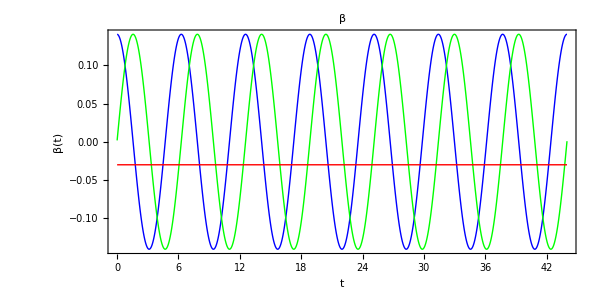

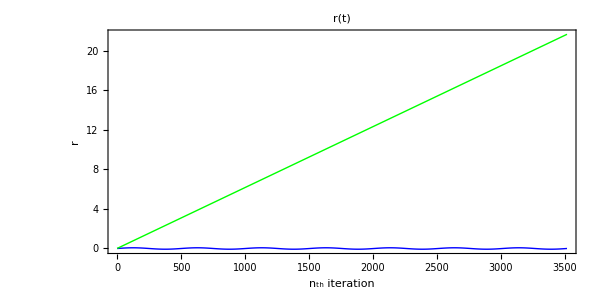

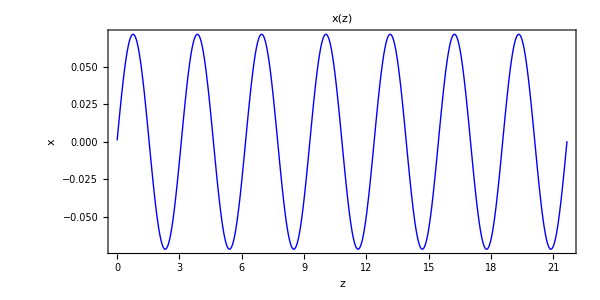

```mathematica
(*Plot*)
ListPlot[{Transpose[{η,βprp[[All,1]]}],
Transpose[{η,βprp[[All,2]]}],
Transpose[{η,βz-1}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Green],Directive[Thick,Red]},Joined->True,AspectRatio->0.5,ImageSize->600,Frame->True,FrameLabel->{"t","β(t)"},PlotRange->All,PlotLabel->"β"]

ListPlot[{x,z},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Green],Directive[Thick,Red]},Joined->True,AspectRatio->0.5,ImageSize->600,Frame->True,FrameLabel->{"n_th iteration","r"},PlotRange->All,PlotLabel->"r(t)"]

ListPlot[Transpose[{z,x}],PlotStyle->{Directive[Thick,Blue],Directive[Thick,Green],Directive[Thick,Red]},Joined->True,AspectRatio->0.5,ImageSize->600,Frame->True,FrameLabel->{"z","x"},PlotRange->All,PlotLabel->"x(z)"]
```

```mathematica
(*Export*)
lst=η;
Dimensions[lst]
Export["dataT.txt",lst,"Table"]

lst=Transpose[{βprp[[All,1]],βprp[[All,2]],βz}];
Dimensions[lst]
Export["dataBETA.txt",lst,"Table"]

lst=Transpose[{x,y,z}];
Dimensions[lst]
Export["dataR.txt",lst,"Table"]
```

{3519}

dataT.txt

{3519,3}

dataBETA.txt

{3519,3}

dataR.txt